```mathematica
otr={{{0,0},{3,0}}};
```

```mathematica
fracLine[otr_List]:=otr/.{a_List,b_List}:>{{a,a+(b-a)/3},{a+(b-a)/3,(a+b)/2+(√3 Reverse[b-a]*{-1,1})/6},{(a+b)/2+(√3 Reverse[b-a]*{-1,1})/6,a+(2(b-a))/3},{a+(2(b-a))/3,b}}//Flatten[#,1]&
```

```mathematica
fracLine[otr]
```

{{{0,0},{1,0}},{{1,0},{3/2,(√3)/2}},{{3/2,(√3)/2},{2,0}},{{2,0},{3,0}}}

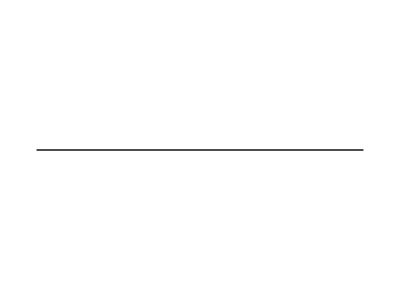
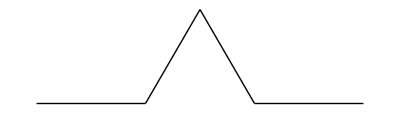
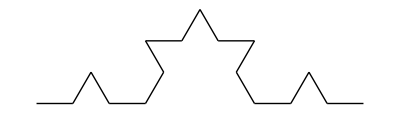

```mathematica
{Graphics[Line[#]&/@otr],Graphics[Line[#]&/@fracLine[otr]],Graphics[Line[#]&/@fracLine[fracLine[otr]]]}
```

```mathematica
NestList[fracLine,otr,5];
```

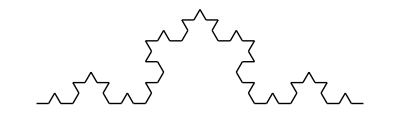
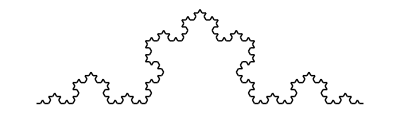
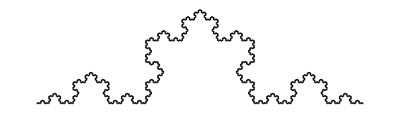
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Graphics[Line[#]&/@#]&/@NestList[fracLine,otr,5]
```